```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
file = Rest[Import["stormofswords.csv"]];
```

```mathematica
tribes = Import["tribes.csv"];
```

```mathematica
nodes =Flatten[tribes[[All,1]]];
```

```mathematica
edges =#[[1]]<->#[[2]]&/@ file [[All,{1,2}]];
```

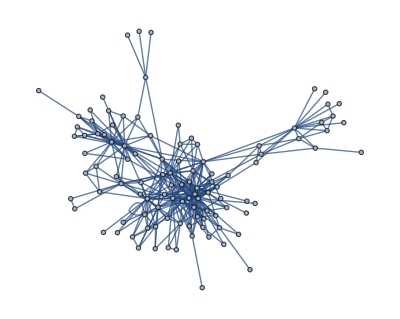

```mathematica
T =Graph[nodes,edges]
```